Laplace transforms is something that Mathematica is good at. Shifting, as far as I can tell, is something that can be routinely shined on.

1 - 16 Laplace transforms
Find the transform. Assume that a, b, ω, θ are constants.

1.  3 t + 12

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=LaplaceTransform[3 t+12,t,s]
```

3/s^2+12/s

The correct answer.

3.  Cos[π t]

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=LaplaceTransform[Cos[π t],t,s]
```

s/(π^2+s^2)

The correct answer.

5.  ⅇ^(2t)Sinh[t]

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=LaplaceTransform[ⅇ^(2 t) Sinh[t],t,s]
```

1/(3-4 s+s^2)

The correct answer.

7.  Sin[ω t + θ]

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=LaplaceTransform[Sin[ω t+θ],t,s]
```

(ω Cos[θ]+s Sin[θ])/(s^2+ω^2)

The correct answer.

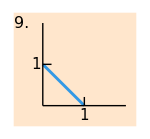

```mathematica
Graphics[{{LightOrange,Rectangle[{-0.7,-0.5},{2.25,2.25}]},{RGBColor[0.2,0.6,0.9],Thickness[0.014],Line[{{0,1},{1,0}}]},{Line[{{0,2},{0,0}}]},{Line[{{0,0},{2,0}}]},{Text[Style["9.",16],{-0.5,2}]},{Line[{{0,1},{0.21,1}}]},{Line[{{1,0},{1,0.21}}]},{Text[Style["1",15],{1,-0.25}]},{Text[Style["1",15],{-0.17,1}]}},ImageSize->150]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=f[t_]=-t+1
```

1-t

```mathematica
e4=LaplaceTransform[If[t>0&&t<1,1-t,0],t,s]
```

(-1+ⅇ^-s+s)/s^2

This is the right answer. There is a big difference on what comes out of the Laplace Transform based on whether the domain is restricted or not.

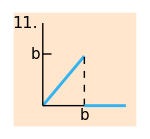

```mathematica
Graphics[{{LightOrange,Rectangle[{-0.7,-0.5},{2.25,2.25}]},{RGBColor[0.2,0.7,0.95],Thickness[0.014],Line[{{0,0},{1,1.2}}]},{Line[{{0,2},{0,0}}]},{Line[{{0,0},{1,0}}]},{Text[Style["11.",16],{-0.42,2}]},{Line[{{0,1.25},{0.21,1.25}}]},{Dashed,Line[{{1,0},{1,1.2}}]},{RGBColor[0.2,0.7,0.95],Thickness[0.014],Line[{{1,0},{2,0}}]},{Text[Style["b",15],{1,-0.25}]},{Text[Style["b",15],{-0.17,1.25}]}},ImageSize->150]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Plot[ 2 x,{x,0,1},PlotRange->Automatic,ImageSize->100,AspectRatio->Automatic]
```

-Graphics-

```mathematica
e1= t
```

t

```mathematica
e2=Simplify[LaplaceTransform[If[t>0&&t<b, t,0],t,s]]
```

Piecewise[{{(ⅇ^(-b s) (-1+ⅇ^(b s)-b s))/s^2, b>0}, {0, True}}]

```mathematica
e3=(ⅇ^(-b s) (-1+ⅇ^(b s)-b s))/s^2
```

(ⅇ^(-b s) (-1+ⅇ^(b s)-b s))/s^2

```mathematica
e4=e3/.( ⅇ^(-b s) (-1+ⅇ^(b s)-b s))->Expand[ ⅇ^(-b s) (-1+ⅇ^(b s)-b s)]
```

(1-ⅇ^(-b s)-b ⅇ^(-b s) s)/s^2

```mathematica
e5=e4/.(1-ⅇ^(-b s)-b ⅇ^(-b s) s)/s^2->(1-ⅇ^(-b s))/s^2-(b ⅇ^(-b s) s)/s^2
```

(1-ⅇ^(-b s))/s^2-(b ⅇ^(-b s))/s

Above: This is the text answer.

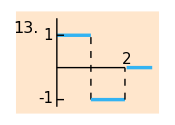

```mathematica
Graphics[{{LightOrange,Rectangle[{-0.7,-0.5},{3.5,2.5}]},{RGBColor[0.2,0.7,0.95],Thickness[0.014],Line[{{0.5,1.8},{1.5,1.8}}]},{Line[{{0.5,2.3},{0.5,-0.3}}]},{Line[{{0.5,0.85},{2.5,0.85}}]},{Text[Style["13.",16],{-0.42,2}]},{Line[{{0.5,1.8},{0.71,1.8}}]},{Line[{{0.5,-0.09},{0.71,-0.09}}]},{Dashed,Line[{{1.5,-0.09},{1.5,1.8}}]},{RGBColor[0.2,0.7,0.95],Thickness[0.014],Line[{{1.5,-0.09},{2.5,-0.09}}]},{Text[Style["-1",15],{0.17,-0.07}]},{Text[Style["1",15],{0.25,1.8}]},{Dashed,Line[{{2.5,-0.09},{2.5,0.85}}]},{Text[Style["2",15],{2.55,1.08}]},{RGBColor[0.2,0.7,0.95],Thickness[0.014],Line[{{2.55,0.85},{3.3,0.85}}]}},ImageSize->175]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=LaplaceTransform[Piecewise[{{1,t>0&&t<1},{-1,t>1&&t<2}}],t,s]
```

-(ⅇ^(-2 s) (-1+ⅇ^s-ⅇ^(2 s)+ⅇ^(2 s) Cosh[s]-ⅇ^(2 s) Sinh[s]))/s

```mathematica
e2=Simplify[e1]
```

(ⅇ^(-2 s) (-1+ⅇ^s)^2)/s

```mathematica
PossibleZeroQ[(ⅇ^(-2 s) (-1+ⅇ^s)^2)/s-((1-ⅇ^-s)^2)/s]
```

True

The above shows that Mathematica's answer and the text answer are equivalent. With a ‘sleight’ maneuver I could even do

```mathematica
e6=e2/.ⅇ^(-2 s) (-1+ⅇ^s)^2->(1-ⅇ^-s)^2
```

((1-ⅇ^-s)^2)/s

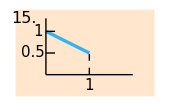

```mathematica
Graphics[{{LightOrange,Rectangle[{-0.7,-0.5},{2.5,1.5}]},{RGBColor[0.2,0.7,0.95],Thickness[0.014],Line[{{0,1},{1,0.5}}]},{Line[{{0,1.3},{0,0}}]},{Line[{{0,0},{2,0}}]},{Text[Style["15.",16],{-0.5,1.3}]},{Line[{{0,1},{0.21,1}}]},{Line[{{0,0.5},{0.21,0.5}}]},{Dashed,Line[{{1,0},{1,0.5}}]},{Text[Style["1",15],{1,-0.25}]},{Text[Style["1",15],{-0.17,1}]},{Text[Style["0.5",15],{-0.3,0.5}]}},ImageSize->170]
```

```mathematica
ClearAll["Global`*"]
```

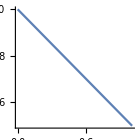

```mathematica
Plot[-1/2 x +1,{x,0,1},PlotRange->Automatic,ImageSize->140,AspectRatio->1]
```

```mathematica
e1=LaplaceTransform[Piecewise[{{-1/2 t +1,t>0&&t<1},{0,t>1&&t<0}}],t,s]
```

(ⅇ^-s (1-ⅇ^s-s+2 ⅇ^s s))/(2 s^2)

```mathematica
e2=TrigToExp[e1]
```

-1/(2 s^2)+ⅇ^-s/(2 s^2)+1/s-ⅇ^-s/(2 s)

The above answer is correct.

21. Nonexistence. Give sample examples of functions (defined for all t ≥ 0) that have no Laplace transform.

If the following expression is true for some constants M and k it satisfies the “growth restriction”

|f(t) ≤ M ⅇ^(k t)|

The sol’n text gives ⅇ^(t^2) as an example. The expression above is a more general guide. The k and M are just constants, so the lhs can overwhelm them if it has an exponential or similar nature.

25 - 32 Inverse Laplace transforms
Given F(s) = L(f), find f(t).  Here a, b, L, n, are constants.

25.  (0.2s+1.8)/(s^2+3.24)

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[(0.2 s+1.8)/(s^2+3.24),s,t]
```

(0.5+0.1 ⅈ) ⅇ^((0.-1.8 ⅈ) t) ((0.384615+0.923077 ⅈ)-(0.+1. ⅈ) ⅇ^((0.+3.6 ⅈ) t))

```mathematica
e2=FullSimplify[e1]
```

ⅇ^((0.-1.8 ⅈ) t) ((0.1+0.5 ⅈ)+(0.1-0.5 ⅈ) ⅇ^((0.+3.6 ⅈ) t))

```mathematica
e3=ExpToTrig[e2]
```

(Cos[(1.8+0. ⅈ) t]-ⅈ Sin[(1.8+0. ⅈ) t]) ((0.1+0.5 ⅈ)+(0.1-0.5 ⅈ) (Cos[(3.6+0. ⅈ) t]+ⅈ Sin[(3.6+0. ⅈ) t]))

```mathematica
e4=FullSimplify[e3]
```

0.2 Cos[1.8 t]+1. Sin[1.8 t]

The above answer matches the text. A bit of work to recast it.

27.  s/(L^2 s^2+n^2 π^2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[s/(L^2 s^2+n^2 π^2),s,t]
```

Cos[(n π t)/L]/L^2

The above answer matches the text.

29.  12/s^4-228/s^6

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[12/s^4-228/s^6,s,t]
```

2 t^3-(19 t^5)/10

The above answer matches the text. Here is demonstrated the linear nature of L^-1: separate fractions can be calculated as a single operand.

31.  (s+10)/(s^2-s-2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[(s+10)/(s^2-s-2),s,t]
```

-3 ⅇ^-t+4 ⅇ^(2 t)

The above answer matches the text.

33 - 45 Application of s-shifting
In problems 33 - 36 find the transform. In problems 37 - 45 find the inverse transform.

33.  t^2 ⅇ^(-3t)

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=LaplaceTransform[t^2 ⅇ^(-3 t),t,s]
```

2/(3+s)^3

The above answer matches the text.

35.  0.5 ⅇ^(-4.5t)Sin[2π t]

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=LaplaceTransform[0.5 ⅇ^(-4.5 t) Sin[2 π t],t,s]
```

3.14159/(4 π^2+(4.5+s)^2)

The above answer matches the text.

37.  π/(s+π)^2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[π/(s+π)^2,s,t]
```

ⅇ^(-π t) π t

The above answer matches the text.

39.  21/(s+√2)^4

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[21/(s+√2)^4,s,t]
```

7/2 ⅇ^(-√2 t) t^3

The above answer matches the text.

41.  π/(s^2+10π s+24 π^2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[π/(s^2+10 π s+24 π^2),s,t]
```

1/2 ⅇ^(-6 π t) (-1+ⅇ^(2 π t))

```mathematica
e2=FullSimplify[ExpToTrig[(-1+ⅇ^(2 π t))/(2  ⅇ^(π t))]]
```

Sinh[π t]

```mathematica
e3=ⅇ^(-5 π t) e2
```

ⅇ^(-5 π t) Sinh[π t]

The above answer matches the text.

43.  (2s-1)/(s^2-6s+18)

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[(2 s-1)/(s^2-6 s+18),s,t]
```

1/6 ⅇ^((3-3 ⅈ) t) ((6+5 ⅈ)+(6-5 ⅈ) ⅇ^(6 ⅈ t))

```mathematica
e2=FullSimplify[e1]
```

1/3 ⅇ^(3 t) (6 Cos[3 t]+5 Sin[3 t])

The above answer matches the text.

45.  (k_0(s+a)+k_1)/(s+a)^2

```mathematica
ClearAll["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[(Subscript[k, 0] (s+a)+Subscript[k, 1])/(s+a)^2,s,t]
```

ⅇ^(-a t) (k_0+t k_1)

The above answer matches the text.

The problems since No. 33 demonstrate that S-shifting doesn’t really exist for Mathematica user.  Just put the expression in and turn the crank.